```mathematica
Clear[h]
```

```mathematica
eq=(Sin[x+h]-Sin[x])/h-Cos[x]==0/.{Sin[x+h]->Series[Sin[x+h],{h,0,5}]}//Simplify
```

-1/2 Sin[x] h-1/6 Cos[x] h^2+1/24 Sin[x] h^3+1/120 Cos[x] h^4+O[h]^5==0

```mathematica
eq2=eq/.Cos[x]->Sqrt[1-Sin[x]^2]
```

-1/2 Sin[x] h-1/6 √(1-Sin[x]^2) h^2+1/24 Sin[x] h^3+1/120 √(1-Sin[x]^2) h^4+O[h]^5==0

```mathematica
eq3=-1/2 Sin[x] h-1/6 √(1-Sin[x]^2) h^2+1/24 Sin[x] h^3+1/120 √(1-Sin[x]^2) h^4==0
```

-1/2 h Sin[x]+1/24 h^3 Sin[x]-1/6 h^2 √(1-Sin[x]^2)+1/120 h^4 √(1-Sin[x]^2)==0

```mathematica
sol=Solve[eq3,Sin[x],Real]
```

Solve::bdomv: Warning: Real is not a valid domain specification. Mathematica is assuming it is a variable to eliminate.

{{Sin[x]→-(h (-20+h^2))/(√(3600-200 h^2-15 h^4+h^6))},{Sin[x]→(h (-20+h^2))/(√(3600-200 h^2-15 h^4+h^6))}}

```mathematica
sol[[1]]
```

{Sin[x]→-(h (-20+h^2))/(√(3600-200 h^2-15 h^4+h^6))}

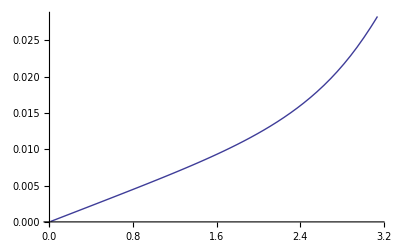

```mathematica
Plot[Evaluate@ArcSin[-h(-20+h^2)/(3600-200h^2-15h^4+h^6)],{h,0.01,Pi}]
```

```mathematica
Series[ArcSin[-h(-20+h^2)/(3600-200h^2-15h^4+h^6)],{h,0,6}]
```

h/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000+O[h]^7

```mathematica
Clear[eqx,h]
```

```mathematica
eqx=h/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000
```

h/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000

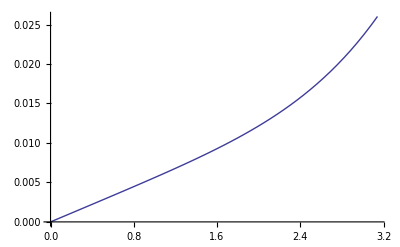

```mathematica
Plot[eqx,{h,0,Pi}]
```

```mathematica
testeq=(Sin[x+h]-Sin[x])/h-Cos[x]
```

-Cos[x]+(-Sin[x]+Sin[h+x])/h

```mathematica
List
```

```mathematica
Plot3D[Evaluate[eq],{x,0,Pi},{h,0.01,2}]
```

-Graphics3D-

```mathematica
data2 = {0.010000,0.000010,0.060000,0.000553,0.110000,0.001929,0.160000,0.004134,0.210000,0.007167,0.260000,0.011023,0.310000,0.015695,0.360000,0.021177,0.410000,0.027460,0.460000,0.034536,0.510000,0.042392,0.560000,0.051019,0.610000,0.060402,0.660000,0.070528,0.710000,0.081382,0.760000,0.092948,0.810000,0.105208,0.860000,0.118144,0.910000,0.131737,0.960000,0.145968,1.010000,0.160814,1.060000,0.176255,1.110000,0.192267,1.160000,0.208828,1.210000,0.225912,1.260000,0.243495,1.310000,0.261552,1.360000,0.280056,1.410000,0.298980,1.460000,0.318298,1.510000,0.337981,1.560000,0.358001,1.610000,0.378331,1.659999,0.398940,1.709999,0.419800,1.759999,0.440882,1.809999,0.462156,1.859999,0.483592,1.909999,0.505160,1.959999,0.526832,2.009999,0.548576,2.059999,0.570364,2.109999,0.592166,2.159999,0.613952,2.209999,0.635694,2.259999,0.657362,2.309999,0.678929,2.359999,0.700366,2.409999,0.721645,2.459999,0.742738,2.509999,0.763620,2.559999,0.784265,2.609999,0.804645,2.659999,0.824737,2.709999,0.844516,2.759999,0.863959,2.809999,0.883042,2.859998,0.901744,2.909998,0.920043,2.959998,0.937919,3.009998,0.955352,3.059998,0.972324,3.109998,0.988818,3.159998,0.988818};
```

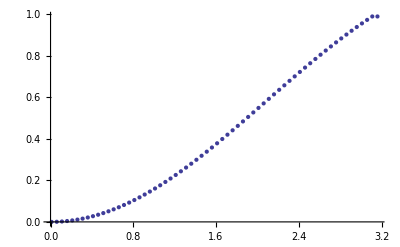

```mathematica
ListPlot[data3]
```

```mathematica
eqx
```

0.0263646

```mathematica
Clear[h]
```

```mathematica
Clear[result]
```

```mathematica
result={};
```

```mathematica
For[h=0.01,h<3.14159,h=h+0.05,result=Append[result,N[eqx]]];
```

```mathematica
result
```

{0.0000555556,0.00033334,0.000611153,0.000889018,0.00116696,0.00144502,0.00172321,0.00200159,0.00228019,0.00255907,0.00283829,0.00311791,0.003398,0.00367866,0.00395999,0.00424209,0.00452509,0.00480912,0.00509435,0.00538094,0.00566907,0.00595896,0.00625081,0.00654489,0.00684144,0.00714076,0.00744315,0.00774894,0.0080585,0.00837219,0.00869043,0.00901366,0.00934233,0.00967694,0.010018,0.0103661,0.0107217,0.0110856,0.0114584,0.0118407,0.0122333,0.0126369,0.0130523,0.0134804,0.013922,0.014378,0.0148495,0.0153374,0.0158427,0.0163665,0.01691,0.0174743,0.0180606,0.0186703,0.0193046,0.0199649,0.0206526,0.0213692,0.0221162,0.0228952,0.0237078,0.0245558,0.0254407}

```mathematica
ls2=Range[0.01,3.14159,0.05]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01,1.06,1.11,1.16,1.21,1.26,1.31,1.36,1.41,1.46,1.51,1.56,1.61,1.66,1.71,1.76,1.81,1.86,1.91,1.96,2.01,2.06,2.11,2.16,2.21,2.26,2.31,2.36,2.41,2.46,2.51,2.56,2.61,2.66,2.71,2.76,2.81,2.86,2.91,2.96,3.01,3.06,3.11}

```mathematica
ls3=Partition[Riffle[ls2,result],2];
```

```mathematica
ls4={ls2,result};
```

```mathematica
testeq1=(Sin[#2+#1]-Sin[#2])/#1-Cos[#2]&
```

(Sin[#2+#1]-Sin[#2])/#1-Cos[#2]&

```mathematica
For[i=1,i<2,i++,Map[testeq1,[ls3[[i,1]],ls3[[i,2]]]]]
```

```mathematica
ls3[[4]]
```

{0.16,0.000889018}

```mathematica
xxxx=MapThread[testeq1,ls4]
```

{-0.0000169444,-0.000609889,-0.00204903,-0.00433218,-0.00745589,-0.0114154,-0.0162048,-0.0218168,-0.028243,-0.0354736,-0.0434978,-0.0523034,-0.0618773,-0.0722051,-0.0832713,-0.0950594,-0.107552,-0.12073,-0.134574,-0.149064,-0.164178,-0.179893,-0.196188,-0.213037,-0.230416,-0.248301,-0.266664,-0.285479,-0.304719,-0.324357,-0.344365,-0.364713,-0.385373,-0.406316,-0.427512,-0.448931,-0.470545,-0.492323,-0.514234,-0.53625,-0.558339,-0.580473,-0.60262,-0.624753,-0.646841,-0.668856,-0.690768,-0.71255,-0.734173,-0.755609,-0.776833,-0.797817,-0.818535,-0.838963,-0.859074,-0.878846,-0.898256,-0.917279,-0.935895,-0.954083,-0.971822,-0.989093,-1.00588}

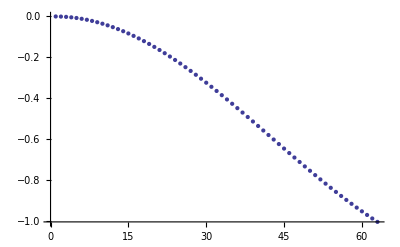

```mathematica
ListPlot[xxxx]
```

```mathematica
Map[testeq1,[ls3[[4,1]],ls3[[4,2]]]]
```

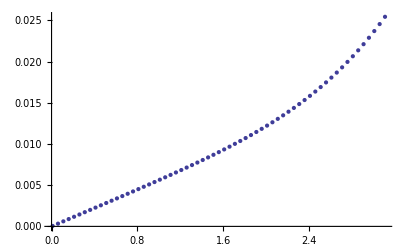

```mathematica
ListPlot[ls3]
```

```mathematica
For[r=0,r<5,r++,xx=Append[result,r]]
```

```mathematica
xx
```

{4}

```mathematica
x1=Append[result,1]
```

{1}

```mathematica
equation=(Sin[x+h]-Sin[x])/h-Cos[x]/.x->eqx
```

-Cos[h/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000]+(-Sin[h/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000]+Sin[(181 h)/180+(1081 h^3)/34992000+(62641201 h^5)/2519424000000])/h

```mathematica
List[N[equation],{h,0.1,Pi}]
```

{-1. Cos[0.00555556 h+0.0000308928 h^3+0.0000248633 h^5]+1/h(-1. Sin[0.00555556 h+0.0000308928 h^3+0.0000248633 h^5]+Sin[1.00556 h+0.0000308928 h^3+0.0000248633 h^5]),{h,0.1,π}}

```mathematica
data4={0.000000,1.000000,-0.158529,1.000000,1.000000,-0.472476,2.000000,1.000000,-0.352031,3.000000,1.000000,0.092070,0.000000,1.050000,-0.173883,1.000000,1.050000,-0.496596,2.000000,1.050000,-0.362742,3.000000,1.050000,0.104616,0.000000,1.100000,-0.189811,1.000000,1.100000,-0.520540,2.000000,1.100000,-0.372687,3.000000,1.100000,0.117813,0.000000,1.150000,-0.206292,1.000000,1.150000,-0.544278,2.000000,1.150000,-0.381857,3.000000,1.150000,0.131642,0.000000,1.200000,-0.223301,1.000000,1.200000,-0.567781,2.000000,1.200000,-0.390246,3.000000,1.200000,0.146079,0.000000,1.250000,-0.240812,1.000000,1.250000,-0.591020,2.000000,1.250000,-0.397847,3.000000,1.250000,0.161105,0.000000,1.300000,-0.258801,1.000000,1.300000,-0.613968,2.000000,1.300000,-0.404656,3.000000,1.300000,0.176696,0.000000,1.350000,-0.277242,1.000000,1.350000,-0.636597,2.000000,1.350000,-0.410668,3.000000,1.350000,0.192828,0.000000,1.400000,-0.296107,1.000000,1.400000,-0.658879,2.000000,1.400000,-0.415881,3.000000,1.400000,0.209477,0.000000,1.450000,-0.315370,1.000000,1.450000,-0.680789,2.000000,1.450000,-0.420294,3.000000,1.450000,0.226618,0.000000,1.500000,-0.335003,1.000000,1.500000,-0.702301,2.000000,1.500000,-0.423907,3.000000,1.500000,0.244226,0.000000,1.549999,-0.354978,1.000000,1.549999,-0.723391,2.000000,1.549999,-0.426721,3.000000,1.549999,0.262274,0.000000,1.599999,-0.375266,1.000000,1.599999,-0.744033,2.000000,1.599999,-0.428739,3.000000,1.599999,0.280735,0.000000,1.649999,-0.395839,1.000000,1.649999,-0.764205,2.000000,1.649999,-0.429965,3.000000,1.649999,0.299583,0.000000,1.699999,-0.416667,1.000000,1.699999,-0.783885,2.000000,1.699999,-0.430402,3.000000,1.699999,0.318790,0.000000,1.749999,-0.437722,1.000000,1.749999,-0.803051,2.000000,1.749999,-0.430058,3.000000,1.749999,0.338328,0.000000,1.799999,-0.458973,1.000000,1.799999,-0.821681,2.000000,1.799999,-0.428939,3.000000,1.799999,0.358167,0.000000,1.849999,-0.480391,1.000000,1.849999,-0.839758,2.000000,1.849999,-0.427055,3.000000,1.849999,0.378281,0.000000,1.899999,-0.501947,1.000000,1.899999,-0.857261,2.000000,1.899999,-0.424413,3.000000,1.899999,0.398638,0.000000,1.949999,-0.523610,1.000000,1.949999,-0.874173,2.000000,1.949999,-0.421025,3.000000,1.949999,0.419211,0.000000,1.999999,-0.545351,1.000000,1.999999,-0.890477,2.000000,1.999999,-0.416903,3.000000,1.999999,0.439970,0.000000,2.049999,-0.567140,1.000000,2.049999,-0.906159,2.000000,2.049999,-0.412060,3.000000,2.049999,0.460885,0.000000,2.099999,-0.588947,1.000000,2.099999,-0.921202,2.000000,2.099999,-0.406508,3.000000,2.099999,0.481928,0.000000,2.149999,-0.610744,1.000000,2.149999,-0.935594,2.000000,2.149999,-0.400263,3.000000,2.149999,0.503068,0.000000,2.199999,-0.632501,1.000000,2.199999,-0.949322,2.000000,2.199999,-0.393341,3.000000,2.199999,0.524276,0.000000,2.249999,-0.654189,1.000000,2.249999,-0.962376,2.000000,2.249999,-0.385759,3.000000,2.249999,0.545523,0.000000,2.299999,-0.675780,1.000000,2.299999,-0.974744,2.000000,2.299999,-0.377533,3.000000,2.299999,0.566780,0.000000,2.349999,-0.697245,1.000000,2.349999,-0.986418,2.000000,2.349999,-0.368683,3.000000,2.349999,0.588017,0.000000,2.399999,-0.718556,1.000000,2.399999,-0.997390,2.000000,2.399999,-0.359228,3.000000,2.399999,0.609207,0.000000,2.449999,-0.739687,1.000000,2.449999,-1.007654,2.000000,2.449999,-0.349188,3.000000,2.449999,0.630320,0.000000,2.499999,-0.760611,1.000000,2.499999,-1.017204,2.000000,2.499999,-0.338585,3.000000,2.499999,0.651328,0.000000,2.549999,-0.781300,1.000000,2.549999,-1.026035,2.000000,2.549999,-0.327438,3.000000,2.549999,0.672204,0.000000,2.599998,-0.801730,1.000000,2.599998,-1.034145,2.000000,2.599998,-0.315772,3.000000,2.599998,0.692920,0.000000,2.649998,-0.821875,1.000000,2.649998,-1.041531,2.000000,2.649998,-0.303609,3.000000,2.649998,0.713450,0.000000,2.699998,-0.841711,1.000000,2.699998,-1.048194,2.000000,2.699998,-0.290972,3.000000,2.699998,0.733768,0.000000,2.749998,-0.861214,1.000000,2.749998,-1.054132,2.000000,2.749998,-0.277886,3.000000,2.749998,0.753847,0.000000,2.799998,-0.880361,1.000000,2.799998,-1.059348,2.000000,2.799998,-0.264376,3.000000,2.799998,0.773662,0.000000,2.849998,-0.899130,1.000000,2.849998,-1.063845,2.000000,2.849998,-0.250466,3.000000,2.849998,0.793190,0.000000,2.899998,-0.917500,1.000000,2.899998,-1.067625,2.000000,2.899998,-0.236181,3.000000,2.899998,0.812407,0.000000,2.949998,-0.935449,1.000000,2.949998,-1.070695,2.000000,2.949998,-0.221549,3.000000,2.949998,0.831288,0.000000,2.999998,-0.952959,1.000000,2.999998,-1.073060,2.000000,2.999998,-0.206594,3.000000,2.999998,0.849813,0.000000,3.049998,-0.970011,1.000000,3.049998,-1.074727,2.000000,3.049998,-0.191344,3.000000,3.049998,0.867960,0.000000,3.099998,-0.986586,1.000000,3.099998,-1.075705,2.000000,3.099998,-0.175825,3.000000,3.099998,0.885707,4.000000,3.149998,0.885707};
```

```mathematica
gi=Partition[Partition[data4,3],4]
```

{{{0.,1.,-0.158529},{1.,1.,-0.472476},{2.,1.,-0.352031},{3.,1.,0.09207}},{{0.,1.05,-0.173883},{1.,1.05,-0.496596},{2.,1.05,-0.362742},{3.,1.05,0.104616}},{{0.,1.1,-0.189811},{1.,1.1,-0.52054},{2.,1.1,-0.372687},{3.,1.1,0.117813}},{{0.,1.15,-0.206292},{1.,1.15,-0.544278},{2.,1.15,-0.381857},{3.,1.15,0.131642}},{{0.,1.2,-0.223301},{1.,1.2,-0.567781},{2.,1.2,-0.390246},{3.,1.2,0.146079}},{{0.,1.25,-0.240812},{1.,1.25,-0.59102},{2.,1.25,-0.397847},{3.,1.25,0.161105}},{{0.,1.3,-0.258801},{1.,1.3,-0.613968},{2.,1.3,-0.404656},{3.,1.3,0.176696}},{{0.,1.35,-0.277242},{1.,1.35,-0.636597},{2.,1.35,-0.410668},{3.,1.35,0.192828}},{{0.,1.4,-0.296107},{1.,1.4,-0.658879},{2.,1.4,-0.415881},{3.,1.4,0.209477}},{{0.,1.45,-0.31537},{1.,1.45,-0.680789},{2.,1.45,-0.420294},{3.,1.45,0.226618}},{{0.,1.5,-0.335003},{1.,1.5,-0.702301},{2.,1.5,-0.423907},{3.,1.5,0.244226}},{{0.,1.55,-0.354978},{1.,1.55,-0.723391},{2.,1.55,-0.426721},{3.,1.55,0.262274}},{{0.,1.6,-0.375266},{1.,1.6,-0.744033},{2.,1.6,-0.428739},{3.,1.6,0.280735}},{{0.,1.65,-0.395839},{1.,1.65,-0.764205},{2.,1.65,-0.429965},{3.,1.65,0.299583}},{{0.,1.7,-0.416667},{1.,1.7,-0.783885},{2.,1.7,-0.430402},{3.,1.7,0.31879}},{{0.,1.75,-0.437722},{1.,1.75,-0.803051},{2.,1.75,-0.430058},{3.,1.75,0.338328}},{{0.,1.8,-0.458973},{1.,1.8,-0.821681},{2.,1.8,-0.428939},{3.,1.8,0.358167}},{{0.,1.85,-0.480391},{1.,1.85,-0.839758},{2.,1.85,-0.427055},{3.,1.85,0.378281}},{{0.,1.9,-0.501947},{1.,1.9,-0.857261},{2.,1.9,-0.424413},{3.,1.9,0.398638}},{{0.,1.95,-0.52361},{1.,1.95,-0.874173},{2.,1.95,-0.421025},{3.,1.95,0.419211}},{{0.,2.,-0.545351},{1.,2.,-0.890477},{2.,2.,-0.416903},{3.,2.,0.43997}},{{0.,2.05,-0.56714},{1.,2.05,-0.906159},{2.,2.05,-0.41206},{3.,2.05,0.460885}},{{0.,2.1,-0.588947},{1.,2.1,-0.921202},{2.,2.1,-0.406508},{3.,2.1,0.481928}},{{0.,2.15,-0.610744},{1.,2.15,-0.935594},{2.,2.15,-0.400263},{3.,2.15,0.503068}},{{0.,2.2,-0.632501},{1.,2.2,-0.949322},{2.,2.2,-0.393341},{3.,2.2,0.524276}},{{0.,2.25,-0.654189},{1.,2.25,-0.962376},{2.,2.25,-0.385759},{3.,2.25,0.545523}},{{0.,2.3,-0.67578},{1.,2.3,-0.974744},{2.,2.3,-0.377533},{3.,2.3,0.56678}},{{0.,2.35,-0.697245},{1.,2.35,-0.986418},{2.,2.35,-0.368683},{3.,2.35,0.588017}},{{0.,2.4,-0.718556},{1.,2.4,-0.99739},{2.,2.4,-0.359228},{3.,2.4,0.609207}},{{0.,2.45,-0.739687},{1.,2.45,-1.00765},{2.,2.45,-0.349188},{3.,2.45,0.63032}},{{0.,2.5,-0.760611},{1.,2.5,-1.0172},{2.,2.5,-0.338585},{3.,2.5,0.651328}},{{0.,2.55,-0.7813},{1.,2.55,-1.02604},{2.,2.55,-0.327438},{3.,2.55,0.672204}},{{0.,2.6,-0.80173},{1.,2.6,-1.03415},{2.,2.6,-0.315772},{3.,2.6,0.69292}},{{0.,2.65,-0.821875},{1.,2.65,-1.04153},{2.,2.65,-0.303609},{3.,2.65,0.71345}},{{0.,2.7,-0.841711},{1.,2.7,-1.04819},{2.,2.7,-0.290972},{3.,2.7,0.733768}},{{0.,2.75,-0.861214},{1.,2.75,-1.05413},{2.,2.75,-0.277886},{3.,2.75,0.753847}},{{0.,2.8,-0.880361},{1.,2.8,-1.05935},{2.,2.8,-0.264376},{3.,2.8,0.773662}},{{0.,2.85,-0.89913},{1.,2.85,-1.06385},{2.,2.85,-0.250466},{3.,2.85,0.79319}},{{0.,2.9,-0.9175},{1.,2.9,-1.06763},{2.,2.9,-0.236181},{3.,2.9,0.812407}},{{0.,2.95,-0.935449},{1.,2.95,-1.0707},{2.,2.95,-0.221549},{3.,2.95,0.831288}},{{0.,3.,-0.952959},{1.,3.,-1.07306},{2.,3.,-0.206594},{3.,3.,0.849813}},{{0.,3.05,-0.970011},{1.,3.05,-1.07473},{2.,3.05,-0.191344},{3.,3.05,0.86796}},{{0.,3.1,-0.986586},{1.,3.1,-1.07571},{2.,3.1,-0.175825},{3.,3.1,0.885707}}}

```mathematica
datalist={}
```

{}

```mathematica
For[x=1,x<50,x=x+10,datalist=Append[datalist,Part[gi,x]]]
```

```mathematica
Flatten@datalist
```

{0.,1.,-0.158529,1.,1.,-0.472476,2.,1.,-0.352031,3.,1.,0.09207,0.,1.5,-0.335003,1.,1.5,-0.702301,2.,1.5,-0.423907,3.,1.5,0.244226,0.,2.,-0.545351,1.,2.,-0.890477,2.,2.,-0.416903,3.,2.,0.43997,0.,2.5,-0.760611,1.,2.5,-1.0172,2.,2.5,-0.338585,3.,2.5,0.651328,0.,3.,-0.952959,1.,3.,-1.07306,2.,3.,-0.206594,3.,3.,0.849813}

```mathematica
datalist2=Partition[Partition[Drop[Flatten@datalist,{2,60,3}],2],4]
```

{{{0.,-0.158529},{1.,-0.472476},{2.,-0.352031},{3.,0.09207}},{{0.,-0.335003},{1.,-0.702301},{2.,-0.423907},{3.,0.244226}},{{0.,-0.545351},{1.,-0.890477},{2.,-0.416903},{3.,0.43997}},{{0.,-0.760611},{1.,-1.0172},{2.,-0.338585},{3.,0.651328}},{{0.,-0.952959},{1.,-1.07306},{2.,-0.206594},{3.,0.849813}}}

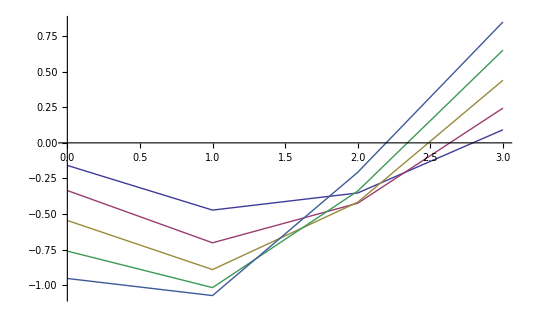

```mathematica
ListLinePlot[datalist2]
```

```mathematica
datalist
```

{{{0.,1.,-0.158529},{1.,1.,-0.472476},{2.,1.,-0.352031},{3.,1.,0.09207}},{{0.,1.5,-0.335003},{1.,1.5,-0.702301},{2.,1.5,-0.423907},{3.,1.5,0.244226}},{{0.,2.,-0.545351},{1.,2.,-0.890477},{2.,2.,-0.416903},{3.,2.,0.43997}},{{0.,2.5,-0.760611},{1.,2.5,-1.0172},{2.,2.5,-0.338585},{3.,2.5,0.651328}},{{0.,3.,-0.952959},{1.,3.,-1.07306},{2.,3.,-0.206594},{3.,3.,0.849813}}}

```mathematica
datalist1
```

{-0.472476,2.,1.,-0.352031,3.,1.,0.09207,0.,1.5,-0.335003,1.,1.5,-0.702301,2.,1.5,-0.423907,3.,1.5,0.244226,0.,2.,-0.545351,1.,2.,-0.890477,2.,2.,-0.416903,3.,2.,0.43997,0.,2.5,-0.760611,1.,2.5,-1.0172,2.,2.5,-0.338585,3.,2.5,0.651328,0.,3.,-0.952959,1.,3.,-1.07306,2.,3.,-0.206594,3.,3.,0.849813}

```mathematica
datalist1={0,-0.158529,1.,1.,-0.472476,2.,1.,-0.352031,3.,1.,0.09207,0.,1.5,-0.335003,1.,1.5,-0.702301,2.,1.5,-0.423907,3.,1.5,0.244226,0.,1.999999,-0.545351,1.,1.999999,-0.890477,2.,1.999999,-0.416903,3.,1.999999,0.43997,0.,2.499999,-0.760611,1.,2.499999,-1.017204,2.,2.499999,-0.338585,3.,2.499999,0.651328,0.,2.999998,-0.952959,1.,2.999998,-1.07306,2.,2.999998,-0.206594,3.,2.999998,0.849813}
```

```mathematica
ListPlot3D[gi]
```

-Graphics3D-